# Digital circuits with CRNs, and the digital abstraction principle

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorExtensions.m"]
```

## Boolean circuits with analog steady-state CRNs

We’ll start by reviewing why the simplest approach doesn’t work.  Consider the bad AND gate, with input species X and Y, and output species Z:  { X + Y  → X + Y + Z, Z → 0 }, which has steady state z = x y where x=[X], y=[Y], and z=[Z].   For any fixed ϵ>0, there is an n such that a circuit of depth n and inputs 1-ϵ will give an output less than ϵ despite that the output should be 1.

```mathematica
badAND[x_,y_]:=x y
```

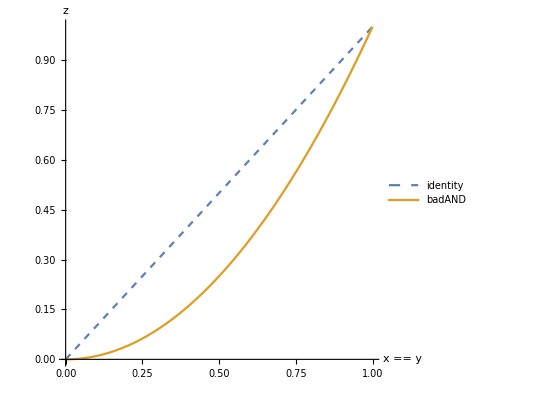

```mathematica
Plot[{x,badAND[x,x]},{x,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Dashed,{}},AxesLabel->{"x == y", "z"},AspectRatio->Equal,PlotLegends->{"identity","badAND"}]
```

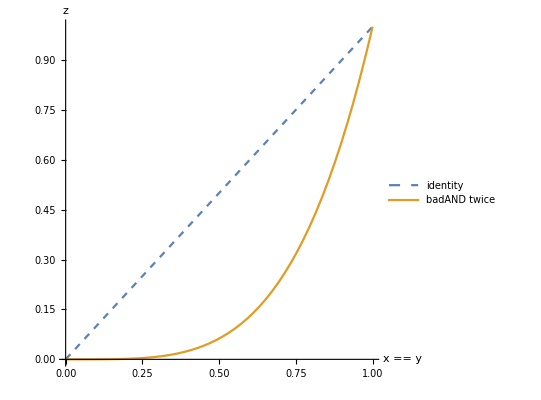

```mathematica
Plot[{x,badAND[badAND[x,x],badAND[x,x]]},{x,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Dashed,{}},AxesLabel->{"x == y", "z"},AspectRatio->Equal,PlotLegends->{"identity","badAND twice"}]
```

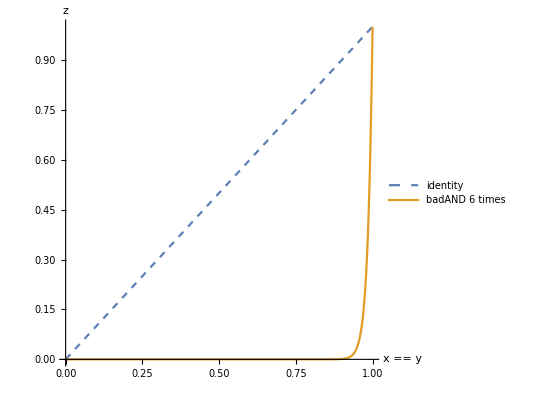

```mathematica
With[{n=6},
Plot[{x,Nest[badAND[#,#]&,x,n]},{x,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Dashed,{}},AxesLabel->{"x == y", "z"},AspectRatio->Equal,PlotLegends->{"identity","badAND "<>ToString[n]<>" times"}]]
```

Now let’s construct CRN modules for Boolean logic gates that work!

For reference, here are the analog steady-state CRN circuit modules that we discussed earlier.   We use them in spirit (i.e. the same principles and constructions, but occasionally making a few simplifications) when constructing the steady-state Boolean logic modules.

```mathematica
CRNconst[A_,v_]:={rxn[0,A,v],rxn[A,0,1]}
CRNcopy[A_,B_]:= {rxn[A,A+B,1],rxn[B,0,1]}
CRNadd[A_,B_,C_]:={rxn[A,A+C,1],rxn[B,B+C,1],rxn[C,0,1]}
CRNsquare[A_,B_]:={rxn[2B,2B+A,1],rxn[A,0,1]}
CRNsqrt[A_,B_]:={rxn[A,A+B,1],rxn[B+B,0,1/2]}
CRNmul[A_,B_,C_]:={rxn[A+B,A+B+C,1],rxn[C,0,1]}
CRNdiv[A_,B_,C_]:={rxn[A,A+C,1],rxn[B+C,B,1]}
CRNrsub[A_,B_,C_]:=Module[{H},{rxn[A,A+C,1],rxn[B,B+H,1],rxn[C,0,1],rxn[C+H,0,1]}]
CRNam[A_,B_]:=Module[{T},{rxn[A+B,A+T,1],rxn[B+A,B+T,1],rxn[T+A,A+A,1],rxn[T+B,B+B,1]}]
```

RESTORE

We give a 4-reaction CRN derived from the desired function form of the input/output relationship.  To illustrate that it satisfied a digital abstraction with tolerance ϵ, we draw a red box delimiting the valid input range and the corresponding valid output range.  Further, we show that simulations (dots) match the analytically predicted steady state.

```mathematica
Simplify[x^2/((1-x)^2+x^2)]
```

x^2/(1-2 x+2 x^2)

```mathematica
CRNrestore[X_,Y_]:={rxn[2X,2X+Y,1],rxn[2X+Y,2X,2],rxn[Y,0,1],rxn[X+Y,X+2Y,2]}
frestore[x_]:=x^2/(1-2x+2x^2)
```

```mathematica
tmax=20;
Manipulate[
sol=SimulateRxnsys[Join[CRNrestore[X,Y],{conc[X,x0]}],tmax];
Plot[Evaluate[{X[t],Y[t]}/.sol],{t,0,tmax},PlotRange->{{0,tmax},{0,1}},PlotStyle->{{Red},{Blue}},PlotLegends->{X,Y},
AxesLabel->{"Time (s)","Concentration (M)"}],
{x0,0,1}]
```

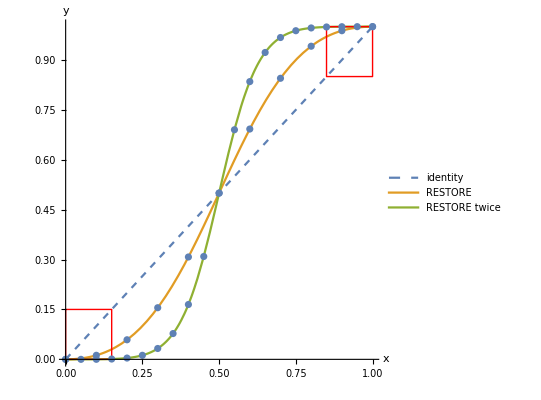

```mathematica
tmax=20;
Show[Plot[{x,frestore[x],frestore[frestore[x]]},{x,0,1},AspectRatio->Equal,PlotStyle->{Dashed,{},{}},PlotLegends->{"identity","RESTORE", "RESTORE twice"},AxesLabel->{x,y}],
With[{ϵ=0.15},Graphics[{Red,Line[{{0,0},{0,ϵ},{ϵ,ϵ},{ϵ,0},{0,0}}],Line[{{1,1},{1,1-ϵ},{1-ϵ,1-ϵ},{1-ϵ,1},{1,1}}]}]],
ListPlot[Table[{x0,Y[tmax]}/.SimulateRxnsys[Join[CRNrestore[X,Y],{conc[X,x0]}],tmax],{x0,0,1,0.1}]],
ListPlot[Table[{x0,Z[tmax]}/.SimulateRxnsys[Join[CRNrestore[X,Y],CRNrestore[Y,Z],{conc[X,x0]}],tmax],{x0,0,1,0.05}]]
]
```

NOT

To invert the output, but otherwise have the same sigmoidal shape as the RESTORE gate, we first compute the RESTORE gate function using intermediate species R, and then subtract that from a constant level of 1 in Y.   (This is essentially CRNrestore[X,R] + CRNconst[S,1] + CRNrsub[S,R,Y] but we rolled up the last two modules into one, so as to avoid needing a second intermediate species.)  Note that the annihilation reaction that carries out the subtraction has a high rate constant -- otherwise, convergence to steady-state can be very slow.

```mathematica
CRNnot[X_,Y_]:=Module[{R,S},{rxn[0,Y,1],rxn[Y,0,1],rxn[R,R+S,1],rxn[S+Y,0,1000]}~Join~CRNrestore[X,R]]
fnot[x_]:=1-frestore[x]
```

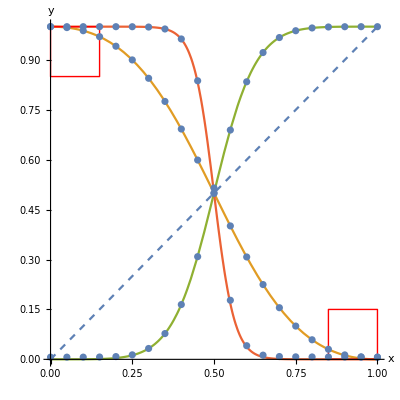

```mathematica
tmax=20; (* the subtraction is very slow near a zero result unless S+Y -> 0 has a high rate constant *)
Show[Plot[{x,fnot[x],fnot[fnot[x]],fnot[fnot[fnot[x]]]},{x,0,1},AspectRatio->Equal,PlotStyle->{Dashed,{},{},{}},AxesLabel->{x,y}],
With[{d=0.15},Graphics[{Red,Line[{{0,1},{0,1-d},{d,1-d},{d,1},{0,1}}],Line[{{1,0},{1,d},{1-d,d},{1-d,0},{1,0}}]}]],
ListPlot[Table[{x0,Y[tmax]}/.SimulateRxnsys[Join[CRNnot[X,Y],{conc[X,x0]}],tmax],{x0,0,1,0.05}]],
ListPlot[Table[{x0,Z[tmax]}/.SimulateRxnsys[Join[CRNnot[X,Y],CRNnot[Y,Z],{conc[X,x0]}],tmax],{x0,0,1,0.05}]],
ListPlot[Table[{x0,W[tmax]}/.SimulateRxnsys[Join[CRNnot[X,Y],CRNnot[Y,Z],CRNnot[Z,W],{conc[X,x0]}],tmax],{x0,0,1,0.05}]]
]
```

AND

This good AND gate is just a bad AND gate followed by a RESTORE gate.   The red boxes in the contour plot indicate the ranges of valid inputs; to the left of the green contour line is where the output exceeds 1-ϵ; to the left of the orange line is where the output remains below ϵ.  Thus, visual inspection establishes the that AND gate satisfies a digital abstraction for this value of ϵ.

```mathematica
CRNand[X_,Y_,Z_]:=Module[{W},{rxn[X+Y,X+Y+W,1],rxn[W,0,1]}~Join~CRNrestore[W,Z]]
fand[x_,y_]:=frestore[x y]
```

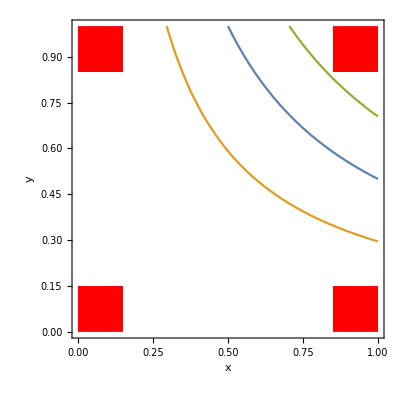

```mathematica
With[{ϵ=0.15},Show[
ContourPlot[{fand[x,y]==0.5,fand[x, y]==ϵ,fand[x, y]==1-ϵ},{x,0,1},{y,0,1},FrameLabel->{x,y}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
overmaxϵ=0.17;
fand[overmaxϵ,overmaxϵ]
1-fand[1-overmaxϵ,1-overmaxϵ]
```

0.000884878

0.169389

```mathematica
CRNand[X,Y,Z]
```

{  X+Y⟶^1W$7946+X+Y,  W$7946⟶^10,  2 W$7946⟶^12 W$7946+Z,  2 W$7946+Z⟶^22 W$7946,  Z⟶^10,  W$7946+Z⟶^2W$7946+2 Z}

```mathematica
tmax=20;
Show[Plot3D[fand[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNand[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

OR

Here the first stage is to compute a scaled sum of X and Y using intermediate species W, and then to fix things up with a RESTORE gate.  The value 0.85 was chosen empirically such that the digital abstraction holds.

```mathematica
CRNor[X_,Y_,Z_]:=Module[{W},{rxn[X,X+W,0.85],rxn[Y,Y+W,.85],rxn[W,0,1]}~Join~CRNrestore[W,Z]]
for[x_,y_]:=frestore[0.85(x+y)]
```

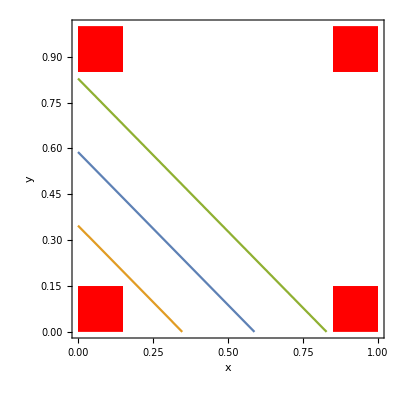

```mathematica
With[{ϵ=0.15},Show[
ContourPlot[{for[x,y]==0.5,for[x, y]==ϵ,for[x, y]==1-ϵ},{x,0,1},{y,0,1},FrameLabel->{x,y}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
overmaxϵ=0.18;
for[overmaxϵ,overmaxϵ]
1-for[1-overmaxϵ,1-overmaxϵ]
```

0.162768

0.0739757

```mathematica
CRNor[X,Y,Z]
```

{  X⟶^0.85W$12034+X,  Y⟶^0.85W$12034+Y,  W$12034⟶^10,  2 W$12034⟶^12 W$12034+Z,  2 W$12034+Z⟶^22 W$12034,  Z⟶^10,  W$12034+Z⟶^2W$12034+2 Z}

```mathematica
tmax=20;
Show[Plot3D[for[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNor[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

XOR

Exclusive-or requires that an “ON” output is generated if and only if exactly one input is “ON”.  If “ON” was represented by +1 and “OFF” by -1, then the output should be minus the product of the inputs, i.e. z = -x y for perfect inputs.  But here we represent “ON” by 1 and “OFF” by 0, so the formula for XOR converts to ±1  and back again.  It simplifies to the difference of a sum and a product.  Again, the rectification aspect of the rectified subtraction never comes into play, because the formula will always be non-negative for non-negative inputs.

```mathematica
Simplify[1-((2x-1)(2y-1)+1)/2]
```

x+y-2 x y

```mathematica
CRNxor[X_,Y_,Z_]:=Module[{S,T},{rxn[X,X+T,1],rxn[Y,Y+T,1],rxn[T,0,1],rxn[X+Y,X+Y+S,2],rxn[T+S,0,1000]}~Join~CRNrestore[T,Z]]
fxor[x_,y_]:=frestore[1-((2x-1)(2y-1)+1)/2]
```

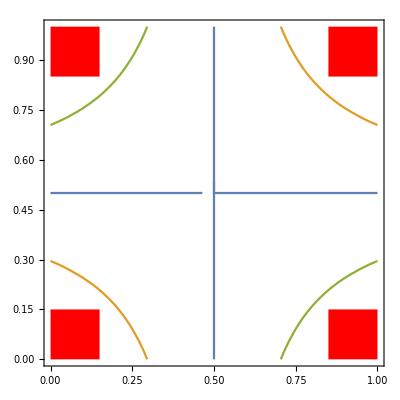

```mathematica
With[{ϵ=0.15},Show[
ContourPlot[{fxor[x,y]==0.5,fxor[x, y]==ϵ,fxor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
CRNxor[X,Y,Z]
```

{  X⟶^1T$16203+X,  Y⟶^1T$16203+Y,  T$16203⟶^10,  X+Y⟶^2S$16203+X+Y,  S$16203+T$16203⟶^10000,  2 T$16203⟶^12 T$16203+Z,  2 T$16203+Z⟶^22 T$16203,  Z⟶^10,  T$16203+Z⟶^2T$16203+2 Z}

```mathematica
tmax=20;
Show[Plot3D[fxor[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNxor[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

XNOR

```mathematica
Simplify[((2x-1)(2y-1)+1)/2]
```

1-y+x (-1+2 y)

```mathematica
CRNxnor[X_,Y_,Z_]:=Module[{S,T},{revrxn[0,T,1,1],rxn[X+Y,X+Y+T,2],rxn[X,X+S,1],rxn[Y,Y+S,1],rxn[T+S,0,1000]}~Join~CRNrestore[T,Z]]
fxnor[x_,y_]:=frestore[((2x-1)(2y-1)+1)/2]
```

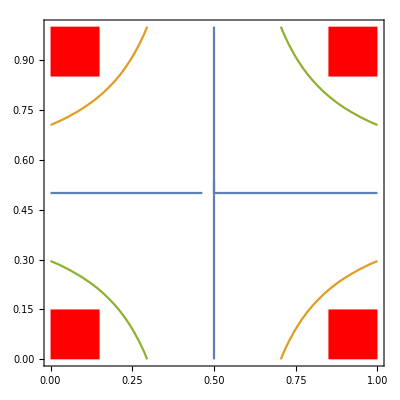

```mathematica
With[{ϵ=0.15},Show[
ContourPlot[{fxnor[x,y]==0.5,fxnor[x, y]==ϵ,fxnor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
CRNxnor[X,Y,Z]
```

{  0⟷_1^1T$20979,  X+Y⟶^2T$20979+X+Y,  X⟶^1S$20979+X,  Y⟶^1S$20979+Y,  S$20979+T$20979⟶^10000,  2 T$20979⟶^12 T$20979+Z,  2 T$20979+Z⟶^22 T$20979,  Z⟶^10,  T$20979+Z⟶^2T$20979+2 Z}

```mathematica
tmax=20;
Show[Plot3D[fxnor[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNxnor[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

This is enough to implement arbitrary feedforward circuits (at least those that only use Not, And, Or, Xor or direct wires).  We borrow the circuit evaluation code and ripple carry adder example from ModelsOfComputation.nb.

```mathematica
CircuitWires[circuit_]:=Union[Flatten[
circuit//.{Rule[wire_,value_]:>{wire,value},(And|Or|Not|Xor|Xnor|Nand|Nor)[args___]:>{args},True|False->{}}]]
```

```mathematica
CircuitStableQ[circuit_,wirevalues_]:=AllTrue[circuit,(#[[1]]/.wirevalues)===(#[[2]]/.wirevalues)&]
```

```mathematica
Truth[0]=False;Truth[1]=True; Attributes[Truth]={Listable};Truth[Rule[LHS_,RHS_]]:=Rule[LHS,Truth[RHS]]
```

```mathematica
CircuitStep[circuit_,wirevalues_]:=
Module[{wires=CircuitWires[circuit],state,n},
state=wires/.wirevalues; (* keep a list of wire values, as True/False in order of "wires" *)
If[!CircuitStableQ[circuit,wirevalues],
n=RandomInteger[{1,Length[state]}];(* randomly try gates until one changes *)
While[state[[n]]==(wires[[n]]/.circuit)/.wirevalues,
n=RandomInteger[{1,Length[state]}]];
state[[n]]=(wires[[n]]/.circuit)/.wirevalues
];
MapThread[Rule,{wires,state}]
]
```

```mathematica
EvaluateCircuit[circuit_,inputvalues_,outputwires_]:=
Module[{wires=CircuitWires[circuit],state,initialwirevalues,finalwirevalues},
(* initialized randomly except for the "inputs" *)
state=Map[If[BooleanQ[#],#,RandomChoice[{True,False}]]&,wires/.inputvalues];
initialwirevalues=MapThread[Rule,{wires,state}];
finalwirevalues=FixedPoint[CircuitStep[circuit,#]&,initialwirevalues];
(* format the out as rules transforming wire names to Boolean values *)
(#->(#/.finalwirevalues))&/@outputwires
]
```

```mathematica
FullAdder[A_,B_,Cin_,S_,Cout_]:=Module[{w1,w2,w3},
{w1->Xor[A,B],S->Xor[Cin,w1],w2->And[w1,Cin],w3->And[A,B],Cout->Or[w2,w3]}]
```

```mathematica
RippleCarryAdder[N_]:=Flatten[Table[FullAdder[A[n],B[n],Cin[n],S[n],Cin[n+1]],{n,0,N-1}]]/.{Cin[0]->False,Cin[N]:>S[N]}
```

```mathematica
AdderCircuitTest[n1_,n2_]:=Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,output},
bits1=IntegerDigits[n1,2,N]//Truth;bits2=IntegerDigits[n2,2,N]//Truth;
output=EvaluateCircuit[RippleCarryAdder[N],
MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}],
Table[S[i],{i,N,0,-1}]]// Boole;
FromDigits[Last/@output,2]
]
```

```mathematica
AdderCircuitTest[17,51]
```

68

To build a CRN from a Boolean circuit, we just need to invoke the right CRN module for each type of logic gate.

```mathematica
CRNcircuit[circuit_]:=Flatten[circuit/.{
(z_->Not[x_]):>CRNnot[x,z],
(z_->And[x_,y_]):>CRNand[x,y,z],
(z_->Or[x_,y_]):>CRNor[x,y,z],
(z_->Xor[x_,y_]):>CRNxor[x,y,z],
(z_->Not[Xor[x_,y_]]):>CRNxnor[x,y,z],
(z_->True):>CRNconst[z,1],
(z_->False):>CRNconst[z,0],
(z_->x_):>CRNrestore[x,z] 
(* watch out, this last case could match too many things!  And it will, if your circuit has something that doesn't the other cases  *)
}]
```

We’ll test it out, starting small.

```mathematica
testcirc={c->Xor[a,b],d->Or[a,b],e->And[c,d]}
```

{c→a⊻b,d→a||b,e→c&&d}

```mathematica
testCRN=CRNcircuit[testcirc]
```

{  a⟶^1a+T$25869,  b⟶^1b+T$25869,  T$25869⟶^10,  a+b⟶^2a+b+S$25869,  S$25869+T$25869⟶^10000,  2 T$25869⟶^1c+2 T$25869,  c+2 T$25869⟶^22 T$25869,  c⟶^10,  c+T$25869⟶^22 c+T$25869,  a⟶^0.85a+W$25870,  b⟶^0.85b+W$25870,  W$25870⟶^10,  2 W$25870⟶^1d+2 W$25870,  d+2 W$25870⟶^22 W$25870,  d⟶^10,  d+W$25870⟶^22 d+W$25870,  c+d⟶^1c+d+W$25871,  W$25871⟶^10,  2 W$25871⟶^1e+2 W$25871,  e+2 W$25871⟶^22 W$25871,  e⟶^10,  e+W$25871⟶^22 e+W$25871}

```mathematica
tmax=200;
With[{ϵ=0.15},
TableForm[Flatten[
Table[{a0,b0,c[tmax],d[tmax],e[tmax]}/.SimulateRxnsys[Join[testCRN,{conc[a,a0],conc[b,b0]}],tmax],
{a0,{ϵ,1-ϵ}},{b0,{ϵ,1-ϵ}}],
1],
TableHeadings->{None,{A,B,Xor,Or,And[Xor,Or]}}]]
```

A | B | Xor | Or | Xor&&Or
0.15 | 0.15 | 0.104871 | 0.104871 | 0.000123642
0.15 | 0.85 | 0.895129 | 0.969799 | 0.977433
0.85 | 0.15 | 0.895129 | 0.969799 | 0.977433
0.85 | 0.85 | 0.104871 | 0.913377 | 0.0110973

Now we verify a CRN for a full adder.

```mathematica
fullcirc=FullAdder[A,B,Cin,S,Cout]
```

{w1$26147→A⊻B,S→Cin⊻w1$26147,w2$26147→w1$26147&&Cin,w3$26147→A&&B,Cout→w2$26147||w3$26147}

```mathematica
fullCRN=CRNcircuit[fullcirc]
```

{  A⟶^1A+T$26149,  B⟶^1B+T$26149,  T$26149⟶^10,  A+B⟶^2A+B+S$26149,  S$26149+T$26149⟶^10000,  2 T$26149⟶^12 T$26149+w1$26147,  2 T$26149+w1$26147⟶^22 T$26149,  w1$26147⟶^10,  T$26149+w1$26147⟶^2T$26149+2 w1$26147,  Cin⟶^1Cin+T$26150,  w1$26147⟶^1T$26150+w1$26147,  T$26150⟶^10,  Cin+w1$26147⟶^2Cin+S$26150+w1$26147,  S$26150+T$26150⟶^10000,  2 T$26150⟶^1S+2 T$26150,  S+2 T$26150⟶^22 T$26150,  S⟶^10,  S+T$26150⟶^22 S+T$26150,  Cin+w1$26147⟶^1Cin+w1$26147+W$26151,  W$26151⟶^10,  2 W$26151⟶^1w2$26147+2 W$26151,  w2$26147+2 W$26151⟶^22 W$26151,  w2$26147⟶^10,  w2$26147+W$26151⟶^22 w2$26147+W$26151,  A+B⟶^1A+B+W$26152,  W$26152⟶^10,  2 W$26152⟶^1w3$26147+2 W$26152,  w3$26147+2 W$26152⟶^22 W$26152,  w3$26147⟶^10,  w3$26147+W$26152⟶^22 w3$26147+W$26152,  w2$26147⟶^0.85w2$26147+W$26153,  w3$26147⟶^0.85w3$26147+W$26153,  W$26153⟶^10,  2 W$26153⟶^1Cout+2 W$26153,  Cout+2 W$26153⟶^22 W$26153,  Cout⟶^10,  Cout+W$26153⟶^22 Cout+W$26153}

```mathematica
tmax=200;
With[{ϵ=0.15},
TableForm[Flatten[
Table[{a0,b0,c0,S[tmax],Cout[tmax]}/.SimulateRxnsys[Join[fullCRN,{conc[A,a0],conc[B,b0],conc[Cin,c0]}],tmax],
{a0,{ϵ,1-ϵ}},{b0,{ϵ,1-ϵ}},{c0,{ϵ,1-ϵ}}],
2],
TableHeadings->{None,{A,B,Cin,S,Cout}}]]
```

A | B | Cin | S | Cout
0.15 | 0.15 | 0.15 | 0.076434 | 4.45706×10^-7
0.15 | 0.15 | 0.85 | 0.923566 | 0.0000737255
0.15 | 0.85 | 0.15 | 0.923566 | 0.00153565
0.15 | 0.85 | 0.85 | 0.076434 | 0.935002
0.85 | 0.15 | 0.15 | 0.923566 | 0.00153565
0.85 | 0.15 | 0.85 | 0.076434 | 0.935002
0.85 | 0.85 | 0.15 | 0.076434 | 0.891075
0.85 | 0.85 | 0.85 | 0.923566 | 0.898836

```mathematica
RippleCarryAdder[2]
```

{w1$26955→A[0]⊻B[0],S[0]→w1$26955,w2$26955→False,w3$26955→A[0]&&B[0],Cin[1]→w2$26955||w3$26955,w1$26956→A[1]⊻B[1],S[1]→w1$26956⊻Cin[1],w2$26956→w1$26956&&Cin[1],w3$26956→A[1]&&B[1],S[2]→w2$26956||w3$26956}

```mathematica
CRNcircuit[RippleCarryAdder[2]]
```

{  A[0]⟶^1T$26959+A[0],  B[0]⟶^1T$26959+B[0],  T$26959⟶^10,  A[0]+B[0]⟶^2S$26959+A[0]+B[0],  S$26959+T$26959⟶^10000,  2 T$26959⟶^12 T$26959+w1$26957,  2 T$26959+w1$26957⟶^22 T$26959,  w1$26957⟶^10,  T$26959+w1$26957⟶^2T$26959+2 w1$26957,  2 w1$26957⟶^12 w1$26957+S[0],  2 w1$26957+S[0]⟶^22 w1$26957,  S[0]⟶^10,  w1$26957+S[0]⟶^2w1$26957+2 S[0],  0⟶^0w2$26957,  w2$26957⟶^10,  A[0]+B[0]⟶^1W$26960+A[0]+B[0],  W$26960⟶^10,  2 W$26960⟶^1w3$26957+2 W$26960,  w3$26957+2 W$26960⟶^22 W$26960,  w3$26957⟶^10,  w3$26957+W$26960⟶^22 w3$26957+W$26960,  w2$26957⟶^0.85w2$26957+W$26961,  w3$26957⟶^0.85w3$26957+W$26961,  W$26961⟶^10,  2 W$26961⟶^12 W$26961+Cin[1],  2 W$26961+Cin[1]⟶^22 W$26961,  Cin[1]⟶^10,  W$26961+Cin[1]⟶^2W$26961+2 Cin[1],  A[1]⟶^1T$26962+A[1],  B[1]⟶^1T$26962+B[1],  T$26962⟶^10,  A[1]+B[1]⟶^2S$26962+A[1]+B[1],  S$26962+T$26962⟶^10000,  2 T$26962⟶^12 T$26962+w1$26958,  2 T$26962+w1$26958⟶^22 T$26962,  w1$26958⟶^10,  T$26962+w1$26958⟶^2T$26962+2 w1$26958,  w1$26958⟶^1T$26963+w1$26958,  Cin[1]⟶^1T$26963+Cin[1],  T$26963⟶^10,  w1$26958+Cin[1]⟶^2S$26963+w1$26958+Cin[1],  S$26963+T$26963⟶^10000,  2 T$26963⟶^12 T$26963+S[1],  2 T$26963+S[1]⟶^22 T$26963,  S[1]⟶^10,  T$26963+S[1]⟶^2T$26963+2 S[1],  w1$26958+Cin[1]⟶^1w1$26958+W$26964+Cin[1],  W$26964⟶^10,  2 W$26964⟶^1w2$26958+2 W$26964,  w2$26958+2 W$26964⟶^22 W$26964,  w2$26958⟶^10,  w2$26958+W$26964⟶^22 w2$26958+W$26964,  A[1]+B[1]⟶^1W$26965+A[1]+B[1],  W$26965⟶^10,  2 W$26965⟶^1w3$26958+2 W$26965,  w3$26958+2 W$26965⟶^22 W$26965,  w3$26958⟶^10,  w3$26958+W$26965⟶^22 w3$26958+W$26965,  w2$26958⟶^0.85w2$26958+W$26966,  w3$26958⟶^0.85w3$26958+W$26966,  W$26966⟶^10,  2 W$26966⟶^12 W$26966+S[2],  2 W$26966+S[2]⟶^22 W$26966,  S[2]⟶^10,  W$26966+S[2]⟶^2W$26966+2 S[2]}

Finally, we adapt the prior test code to test if the CRN can add arbitrary numbers.  A large enough Boolean circuit is constructed and then converted to a CRN, which is then run for the binary inputs representing the two numbers, and finally the output is collected, tested to make sure it’s valid, and interpreted as a resulting integer.  This verifies by example that the digital abstraction is working -- the imperfect input does not derail the computation, even in large circuits!

```mathematica
AdderCRNTest[n1_,n2_,ϵ_]:=Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,inputwires,inputconcs,output,rsys,tmax},
bits1=IntegerDigits[n1,2,N];bits2=IntegerDigits[n2,2,N];
circuit=RippleCarryAdder[N];
Print["Boolean circuit has ",Length[circuit]," gates and ",Length[CircuitWires[circuit]]," wires."];
rsys=CRNcircuit[circuit];tmax=100N; 
Print["CRN contains ",Length[rsys]," reactions and ",Length[SpeciesInRxnsys[rsys]]," species and can add any two ",N," bit integers."];
inputwires=MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}];
inputconcs=conc[First[#],Last[#]/.{0->ϵ,1->1-ϵ}]&/@inputwires;
output=Table[S[i][tmax],{i,N,0,-1}]/.SimulateRxnsys[Join[rsys,inputconcs],tmax];
Print["Inputs are off by at most ",ϵ," and outputs are off by at most ",Max[Min[#,1-#]&/@output],"."];
Print["The sum of ",n1," and ",n2," should be ",n1+n2,"."];
FromDigits[If[#<ϵ,0,If[#>1-ϵ,1,NaN]]&/@output,2]
]
```

```mathematica
AdderCRNTest[RandomInteger[10^8],RandomInteger[10^8],.15]
```

Boolean circuit has 135 gates and 189 wires.

CRN contains 990 reactions and 375 species and can add any two 27 bit integers.

Inputs are off by at most 0.15 and outputs are off by at most 0.109144.

The sum of 67355614 and 91161622 should be 158517236.

158517236

### Some relevant references

Magnasco, Marcelo O. “Chemical kinetics is Turing universal.” Physical Review Letters 78, no. 6 (1997): 1190.Harvard
Jiang, Hua, Marc D. Riedel, and Keshab K. Parhi. “Digital logic with molecular reactions.” In 2013 IEEE/ACM International Conference on Computer-Aided Design (ICCAD), pp. 721-727. IEEE, 2013.